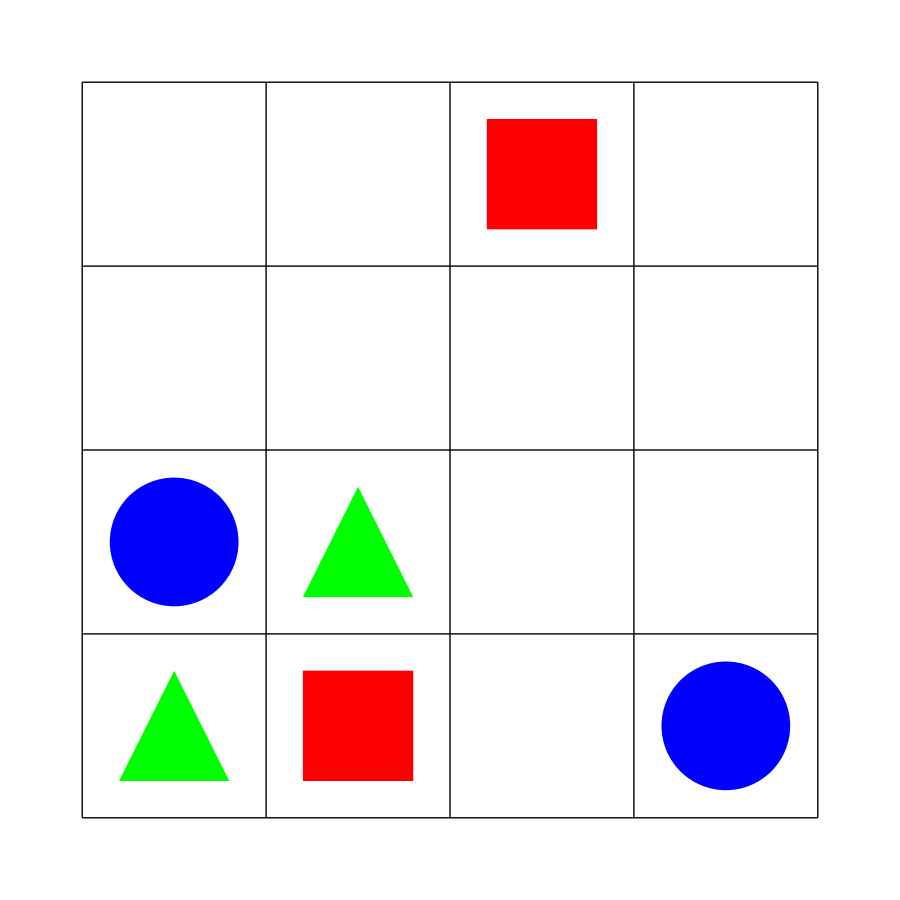

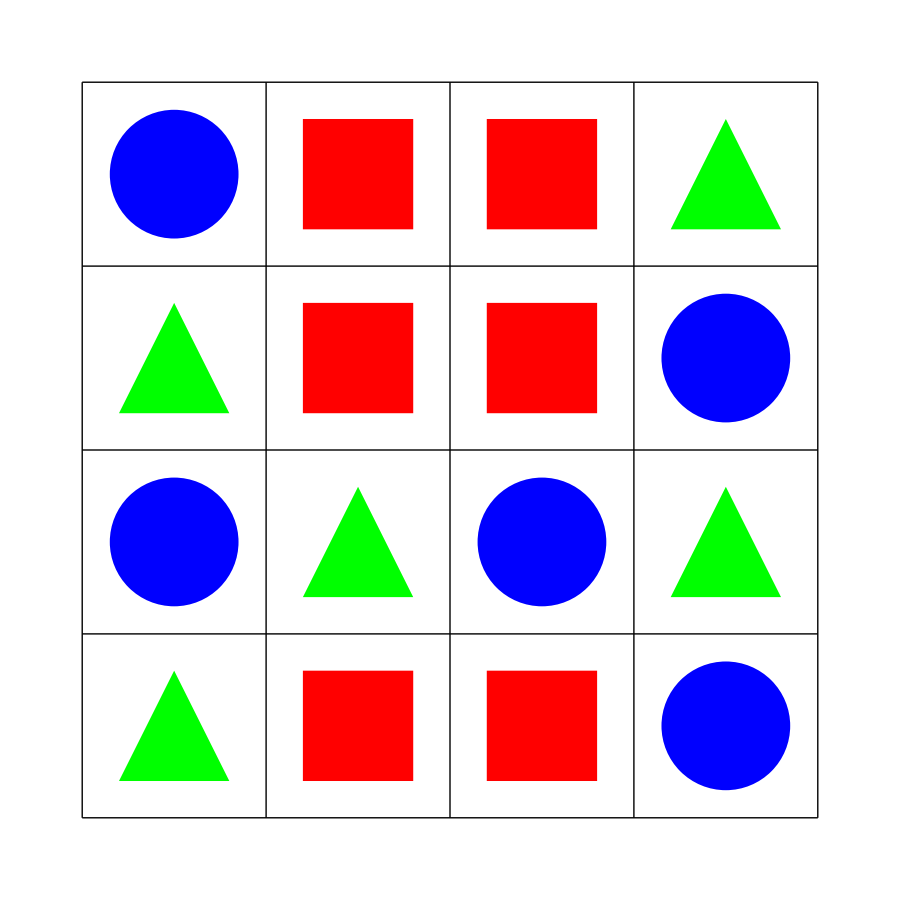

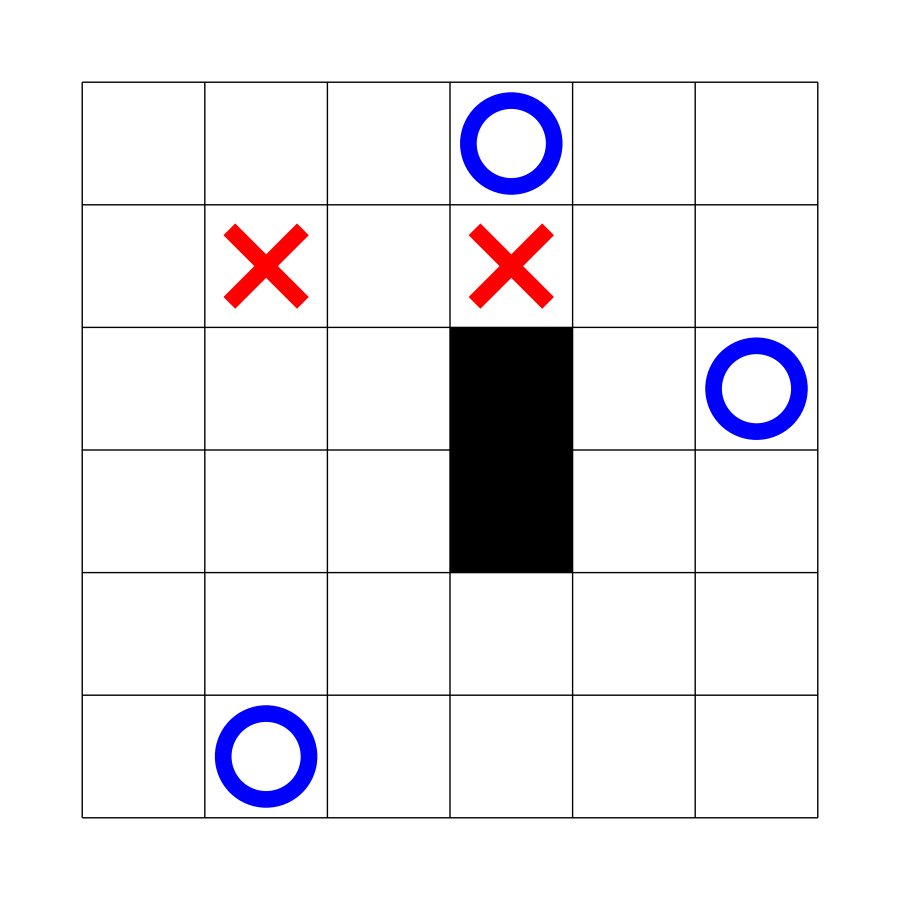

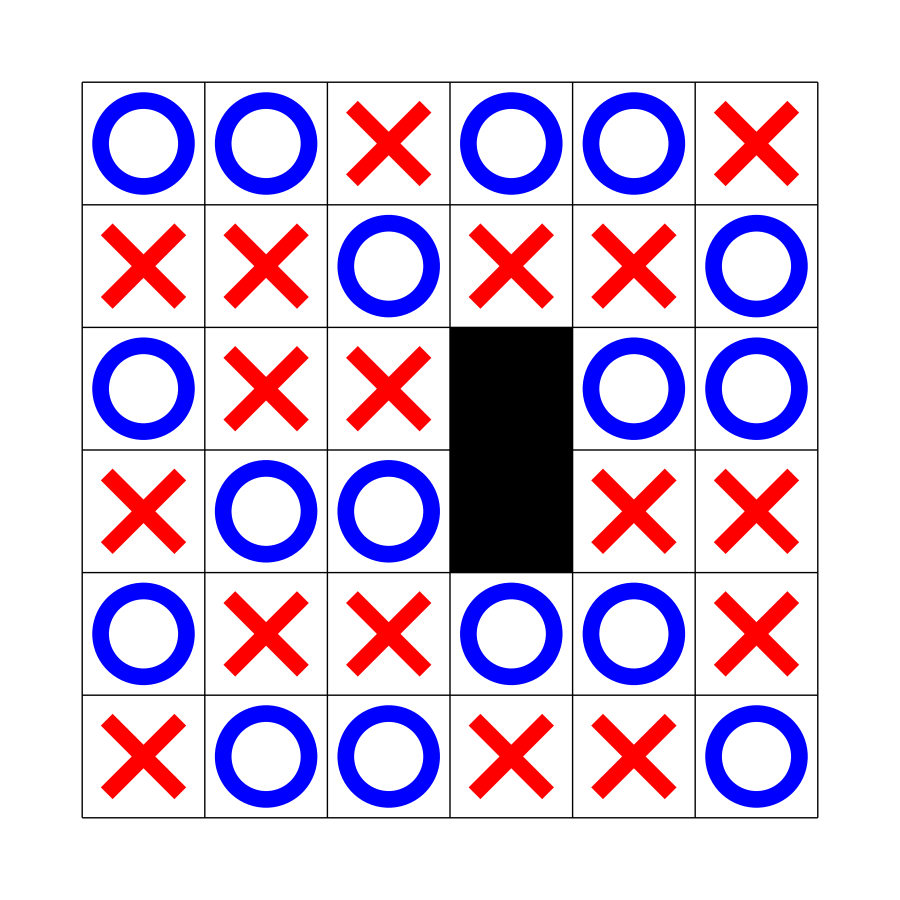

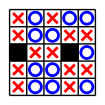

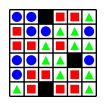

```mathematica
pic[A_]:=Graphics[{
Style[{Table[Line[{{i,0},{i,Length[A[[1]]]}}],{i,0,Length[A]}],Table[Line[{{0,i},{Length[A],i}}],{i,0,Length[A[[1]]]}]},Antialiasing->False],AbsoluteThickness[2],
MapIndexed[Which[#1==1,{Red,Line[{#2-{.8,.8},#2-{.2,.2}}],Line[{#2-{.2,.8},#2-{.8,.2}}]},#1==2,{Blue,Circle[#2-{.5,.5},.35]},#1==-1,{Black,Rectangle[#2-1,#2]},True,{}]&,A,{2}]
},ImageSize->20Dimensions[A]]
(* tic tac toe *)
```

```mathematica
pic[A_]:=Graphics[{
Style[{Table[Line[{{i,0},{i,Length[A[[1]]]}}],{i,0,Length[A]}],Table[Line[{{0,i},{Length[A],i}}],{i,0,Length[A[[1]]]}]},Antialiasing->False],AbsoluteThickness[2],
MapIndexed[Which[#1==1,{Red,Rectangle[#2-{.8,.8},#2-{.2,.2}]},#1==2,{Blue,Disk[#2-{.5,.5},.35]},#1==3,{Green,Polygon[{#2-{.8,.8},#2-{.2,.8},#2-{.5,.2}}]},#1==-1,{Black,Rectangle[#2-1,#2]},True,{}]&,A,{2}]
},ImageSize->20Dimensions[A]]
(* shapes *)
```

```mathematica
beforepic[L_]:=Graphics[{
Style[{Table[Line[{{i,0},{i,m}}],{i,0,n}],Table[Line[{{0,i},{n,i}}],{i,0,m}]},Antialiasing->False],AbsoluteThickness[2],
Map[If[#[[2]]==1,{Red,Line[{#[[1]]-{.8,.8},#[[1]]-{.2,.2}}],Line[{#[[1]]-{.2,.8},#[[1]]-{.8,.2}}]},{Blue,Circle[#[[1]]-{.5,.5},.35]}]&,L],
MapIndexed[If[#1==-1,{Black,Rectangle[#2-1,#2]},{}]&,A,{2}]
},ImageSize->20{n,m}]
(* tic tac toe *)
```

```mathematica
beforepic[L_]:=Graphics[{
Style[{Table[Line[{{i,0},{i,m}}],{i,0,n}],Table[Line[{{0,i},{n,i}}],{i,0,m}]},Antialiasing->False],AbsoluteThickness[2],
Map[Which[#[[2]]==1,{Red,Rectangle[#[[1]]-{.8,.8},#[[1]]-{.2,.2}]},#[[2]]==2,{Blue,Disk[#[[1]]-{.5,.5},.35]},#[[2]]==3,{Green,Polygon[{#[[1]]-{.8,.8},#[[1]]-{.2,.8},#[[1]]-{.5,.2}}]},True,{}]&,L],
MapIndexed[If[#1==-1,{Black,Rectangle[#2-1,#2]},{}]&,A,{2}]
},ImageSize->20{n,m}]
(* shapes *)
```

```mathematica
mirror[line_,A_]:=Map[Dimensions[A]+1-#&,line]
```

```mathematica
allsame[L_]:=Length[Union[L]]==1 (* tic tac toe *)
```

```mathematica
allsame[L_]:=(Length[Union[L]]==1 )||(Union[L]=={1,2,3})(* shapes *)
```

```mathematica
possibleQ[A_,loc_,sym_]:=Module[{},
AA=ReplacePart[A,loc->sym];
lines={{loc-{2,2},loc-{1,1},loc},{loc-{1,1},loc,loc+{1,1}},{loc,loc+{1,1},loc+{2,2}},{loc-{2,0},loc-{1,0},loc},{loc-{1,0},loc,loc+{1,0}},{loc,loc+{1,0},loc+{2,0}},{loc+{2,-2},loc+{1,-1},loc},{loc+{1,-1},loc,loc+{-1,1}},{loc,loc+{-1,1},loc+{-2,2}},{loc-{0,2},loc-{0,1},loc},{loc-{0,1},loc,loc+{0,1}},{loc,loc+{0,1},loc+{0,2}}};
real=Select[lines,Apply[Times,Flatten[#]]>0&& Apply[Times,Flatten[mirror[#,A]]]>0&];
Apply[Or,Map[allsame[Extract[AA,#]]&,real]]
]
```

```mathematica
build[A_,clues_]:=Module[{},
B=Table[0,{n},{m}];
For[i=1,i≤Length[clues],i++,
B=ReplacePart[B,clues[[i,1]]->clues[[i,2]]]];
blocks=Position[A,-1];
For[i=1,i≤Length[blocks],i++,
B=ReplacePart[B,blocks[[i]]->-1]];B]
```

```mathematica
findsolutions[A_]:=Module[{cur,z,pos,pp},
solns={};
stac={A};
While[Length[stac]>0,
cur=First[stac];
stac=Rest[stac];
z=Position[cur,0];
If[z=={},AppendTo[solns,cur],
pos=z[[1]];
pp=possibles[cur,pos];
qq=Map[ReplacePart[cur,pos->#]&,pp];
stac=Join[qq,stac]]];
solns]
```

```mathematica
possibles[A_,loc_]:=Module[{},
temp={};
If[Not[possibleQ[A,loc,1]],temp={1}];
If[Not[possibleQ[A,loc,2]],AppendTo[temp,2]];
temp]
(* tic tac toe *)
```

```mathematica
possibles[A_,loc_]:=Module[{},
temp={};
If[Not[possibleQ[A,loc,1]],temp={1}];
If[Not[possibleQ[A,loc,2]],AppendTo[temp,2]];
If[Not[possibleQ[A,loc,3]],AppendTo[temp,3]];
temp]
(* shapes *)
```

```mathematica
n=9;m=n;maxblock=Floor[n^2/10]+2;
For[k=1,k>0,k++,
A=Table[0,{n},{m}];
clues={};
While[(c=Count[Flatten[A],0])>0,
r=RandomInteger[{1,c}];
pos=Position[A,0][[r]];
q=possibles[A,pos];
If[Length[q]==1,A=ReplacePart[A,pos->q[[1]]]];
If[q=={},A=ReplacePart[A,pos->-1]];
If[Length[q]==2,d=RandomInteger[{1,2}];A=ReplacePart[A,pos->d];AppendTo[clues,{pos,d}]]];
If[Count[Flatten[A],-1]≤maxblock,For[j=1,j≤Length[clues],j++,
If[Length[findsolutions[build[A,Drop[clues,{j}]]]]==1,clues=Drop[clues,{j}];j--]];
If[Length[clues]+Count[Flatten[A],-1]<.25n m,
Print[beforepic[clues]];
Print[pic[A]]]]];
(* tic tac toe *)
```

$Aborted

```mathematica
n=8;m=n;maxblock=4;
For[k=1,k>0,k++,
A=Table[0,{n},{m}];
clues={};
While[(c=Count[Flatten[A],0])>0,
r=RandomInteger[{1,c}];
pos=Position[A,0][[r]];
q=possibles[A,pos];
If[q=={},A=ReplacePart[A,pos->-1],d=RandomInteger[{1,Length[q]}];A=ReplacePart[A,pos->q[[d]]];If[Length[q]>1,AppendTo[clues,{pos,q[[d]]}]]]];
If[Count[Flatten[A],1]>.2n m&&Count[Flatten[A],2]>.2n m&&Count[Flatten[A],3]>.2n m&&Count[Flatten[A],-1]≤maxblock,
For[j=1,j≤Length[clues],j++,
If[Length[findsolutions[build[A,Drop[clues,{j}]]]]==1,clues=Drop[clues,{j}];j--]];
If[Length[clues]+Count[Flatten[A],-1]<.4n m,
Print[beforepic[clues]];
Print[pic[A]]]]];
(* shapes *)
```

## 5x5 tic

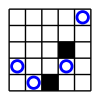

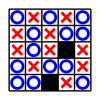

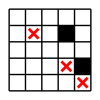

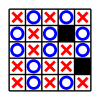

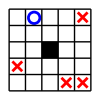

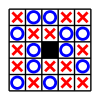

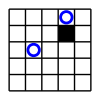

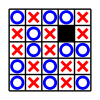

## 6x6 tic

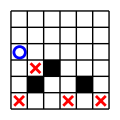

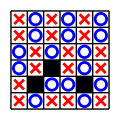

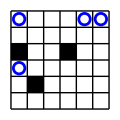

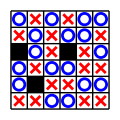

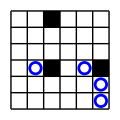

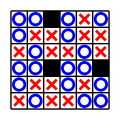

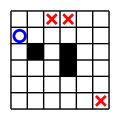

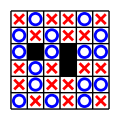

-Graphics-

-Graphics-

-Graphics-

«91 more identical outputs»

## 7x7 tic

-Graphics-

-Graphics-

-Graphics-

«113 more identical outputs»

## 8x8 tic

-Graphics-

-Graphics-

-Graphics-

«67 more identical outputs»

## 9x9 tic

-Graphics-

-Graphics-

-Graphics-

«91 more identical outputs»

## 4x4 shapes

-Graphics-

-Graphics-

-Graphics-

«143 more identical outputs»

## 5x5 shapes

-Graphics-

-Graphics-

-Graphics-

«103 more identical outputs»

## 6x6 shapes

-Graphics-

-Graphics-

-Graphics-

«53 more identical outputs»

## 7x7 shapes

-Graphics-

-Graphics-

-Graphics-

«51 more identical outputs»

## 8x8 shapes

-Graphics-

-Graphics-

-Graphics-

«29 more identical outputs»

## 9x9 shapes

-Graphics-

-Graphics-

-Graphics-

«25 more identical outputs»